## Min Heap Implementation

I will implement a min-Heap using a list a. The Heap will store tuples {t, i}, where t is the time of the next collision including particle i.

### HeapQ

Tests if a is a min-Heap in O(N).

#### Definition

```mathematica
HeapQ[a_List]:=Module[{n=a//Length},
And@@Table[a⟦Floor[i/2]⟧≤ a⟦i⟧, {i, 2, n}]
]
```

#### Testing

```mathematica
a=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
HeapQ[a]
```

True

### HSwap

#### Definition

Function swaps elements i and j of list a. Argument a has to be in variable (unevaluated) form

```mathematica
HSwap=Function[{a, i, j},
{a⟦i⟧, a⟦j⟧}={a⟦j⟧, a⟦i⟧};,
HoldFirst];
```

```mathematica
HSwap2=Function[{a, i, j},
{a⟦i⟧, a⟦j⟧}={a⟦j⟧, a⟦i⟧};
a];
```

#### Testing

```mathematica
a={1,2,3}
```

{1,2,3}

```mathematica
a=HSwap2[Unevaluated@a, 1, 2]
```

{2,1,3}

```mathematica
a
```

{2,1,3}

```mathematica
x={1, 2, 3};
HSwap[x,1,3]
```

```mathematica
x
```

{3,2,1}

```mathematica
Clear[a, i, j]
```

```mathematica
a={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
a[[1]]=a[[4]]
```

4

```mathematica
a[[1]]
```

4

```mathematica
HSwap[a, 1, 4]
```

Set::setps: {4,2,3,4,5} in the part assignment is not a symbol.

4

### HeapifyDown

Recursively updates downwards, following minHeap property.

#### Definition

```mathematica
HeapifyDown=Function[{a, i},
Module[{ n=a//Length},
Which[n<2i,
	a,
	(*at leaf*)
	n≤2i && a⟦i⟧≥ a⟦2i⟧, 
	{a⟦i⟧, a⟦2i⟧}={a⟦2i⟧, a⟦i⟧};
	HeapifyDown[a, 2i];,
	(*only left child*)
	a⟦i⟧≤ a⟦2i⟧ && a⟦i⟧≤ a⟦2i+1⟧, 
	a,
	(*property satisfied*)
	a⟦i⟧≥Min[a⟦2i⟧, a⟦2i+1⟧] && a⟦2i⟧≤  a⟦2i+1⟧,
	{a⟦i⟧, a⟦2i⟧}={a⟦2i⟧, a⟦i⟧};
	HeapifyDown[a, 2i];,
	(*swap with left child*)
	a⟦i⟧≥  Min[a⟦2i⟧, a⟦2i+1⟧] && a⟦2i⟧>a⟦2i+1⟧,
	{a⟦i⟧, a⟦2i+1⟧}={a⟦2i+1⟧, a⟦i⟧};
	HeapifyDown[a, 2i+1];
	(*swap with right child*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
a={10,1,2,3,4}
```

{10,1,2,3,4}

```mathematica
a⟦1⟧
```

10

```mathematica
HeapifyDown[a, 1]
```

```mathematica
a//HeapQ
```

True

### HeapifyUp

Recursively updates upwards, following minHeap property

```mathematica
HeapifyUp=Function[{a, i},
Module[{ n=a//Length},
Which[
i==1,
a,
(*at root*)
a⟦i⟧≥ a⟦Floor[i/2]⟧,
a,
(*satisfies minHeap prop, return*)
a⟦i⟧≤ a⟦Floor[i/2]⟧,
{a⟦i⟧, a⟦Floor[i/2]⟧}={a⟦Floor[i/2]⟧, a⟦i⟧};
HeapifyUp[a, Floor[i/2]];
(*swap with parent, if greater*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
a={1,2,3,4,5,6,7,1};
HeapifyUp[a, 8]
```

```mathematica
a//HeapQ
```

True

### Insert

This function appends the element to the end of the min-heap, and places it with HeapifyUp.

#### Definition

```mathematica
HInsert=Function[{H, element},
AppendTo[H, element];
HeapifyUp[H, H//Length];,
HoldFirst
];
```

#### Testing

```mathematica
h={1,2,3,4,5,6};
```

```mathematica
HInsert[h, 1]
```

```mathematica
h
```

{1,2,1,4,5,6,3}

### extractMin

#### Definition

```mathematica
extractMin=Function[{H},
Module[{last},
HSwap[H,1, H//Length];
last=H⟦-1⟧;
H=Most@H;
HeapifyDown[H, 1];
last
],
HoldFirst
];
```

### Testing

```mathematica
h=Range[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
extractMin[h]
```

1

```mathematica
h//HeapQ
```

HeapQ[{2,4,3,8,5,6,7,16,9,10,11,12,13,14,15,32,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,64,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,100,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99}]

## Scratch

```mathematica
l={1,2,3,4,5,6}
```

{1,2,3,4,5,6}

```mathematica
Most[l]
```

{1,2,3,4,5}

```mathematica
l
```

{1,2,3,4,5,6}

```mathematica
tester=Table[(extractMin[Range[10^n]]//AbsoluteTiming)⟦1⟧, {n, 3}]
```

Set::setps: Range[10^n] in the part assignment is not a symbol.

Set::write: Tag Range in Range[10] is Protected.

Set::setps: Range[10^n] in the part assignment is not a symbol.

General::stop: Further output of Set::setps will be suppressed during this calculation.

Set::write: Tag Range in Range[100] is Protected.

Set::write: Tag Range in Range[1000] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

{0.00354587,0.00322606,0.00220243}

```mathematica
t=Table[Range[10^i], {i, 7}];
```

```mathematica
v=Table[(extractMin[t⟦i⟧]//AbsoluteTiming)⟦1⟧, {i,7}];
```

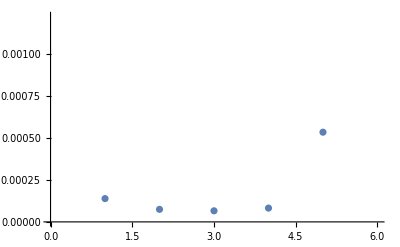

```mathematica
v//ListPlot
```

```mathematica
l=Range[10^6]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,999880,999941,999942,999943,999944,999945,999946,999947,999948,999949,999950,999951,999952,999953,999954,999955,999956,999957,999958,999959,999960,999961,999962,999963,999964,999965,999966,999967,999968,999969,999970,999971,999972,999973,999974,999975,999976,999977,999978,999979,999980,999981,999982,999983,999984,999985,999986,999987,999988,999989,999990,999991,999992,999993,999994,999995,999996,999997,999998,999999,1000000}
 |  |  |  |

```mathematica
ClearSystemCache
```

ClearSystemCache

```mathematica
l=Range[10^2];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

0.000478396

```mathematica
l=Range[10^3];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

0.000714384

```mathematica
l=Range[10^4];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

0.000626408

```mathematica
l=Range[10^5];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

0.00154997

```mathematica
l=Range[10^8];
(extractMin[l]//AbsoluteTiming)⟦1⟧
```

General::nomem: The current computation was aborted because there was insufficient memory available to complete the computation.

Throw::sysexc: Uncaught SystemException returned to top level. Can be caught with Catch[…, _SystemException].

SystemException[MemoryAllocationFailure]

```mathematica
l=RandomReal[10, 1000]//Sort;
```

```mathematica
(l//extractMin//AbsoluteTiming)⟦1⟧
```

0.000720803

```mathematica
l4=RandomReal[10, 10000]//Sort;
```

```mathematica
(l4//extractMin//AbsoluteTiming)⟦1⟧
```

0.00105987

```mathematica
l5=RandomReal[10, 100000]//Sort;
```

```mathematica
(l5//extractMin//AbsoluteTiming)⟦1⟧
```

0.000942444

```mathematica
l6=RandomReal[10, 1000000]//Sort;
```

```mathematica
(l6//extractMin//AbsoluteTiming)⟦1⟧
```

0.023048

```mathematica
l7=RandomReal[10, 10000000]//Sort;
```

```mathematica
(l7//extractMin//AbsoluteTiming)⟦1⟧
```

0.172846

```mathematica
Clear[]
```

## New Implementation

```mathematica
heap=Range[100];
```

### heapQnew

Tests if a is a min-Heap in O(N).

#### Definition

```mathematica
heapQnew[a_List]:=Module[{n=a//Length},
And@@Table[a⟦Floor[i/2]⟧≤ a⟦i⟧, {i, 2, n}]
]
```

#### Testing

```mathematica
a=Range[10];
```

```mathematica
heapQnew[a]
```

True

### heapswapnew

Swaps elements i and j of heap.

#### Definition

```mathematica
heapswapnew[i_,j_]:={heap⟦i⟧, heap⟦j⟧}={heap⟦j⟧, heap⟦i⟧};
```

#### Testing

```mathematica
heapswapnew[1, 2];
```

```mathematica
heap
```

{2,1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
heapswapnew[1, 2];
```

### heapifyDownnew

#### Definition

```mathematica
heapifyDownnew=Function[{i},
Module[{ n=heap//Length},
Which[n<2i,
	heap,
	(*at leaf*)
	n≤2i && heap⟦i⟧≥ heap⟦2i⟧, 
	{heap⟦i⟧, heap⟦2i⟧}={heap⟦2i⟧, heap⟦i⟧};
	heapifyDownnew[2i];,
	(*only left child*)
	n≤2i && heap⟦i⟧≤  heap⟦2i⟧, 
	heap,
	(*only left child, satisfied*)
	heap⟦i⟧≤ heap⟦2i⟧ && heap⟦i⟧≤ heap⟦2i+1⟧, 
	heap,
	(*property satisfied*)
	heap⟦i⟧≥Min[heap⟦2i⟧, heap⟦2i+1⟧] && heap⟦2i⟧≤  heap⟦2i+1⟧,
	{heap⟦i⟧, heap⟦2i⟧}={heap⟦2i⟧, heap⟦i⟧};
	heapifyDownnew[2i];,
	(*swap with left child*)
	heap⟦i⟧≥  Min[heap⟦2i⟧, heap⟦2i+1⟧] && heap⟦2i⟧>heap⟦2i+1⟧,
	{heap⟦i⟧, heap⟦2i+1⟧}={heap⟦2i+1⟧, heap⟦i⟧};
	heapifyDownnew[2i+1];
	(*swap with right child*)
 ]
]
];
```

#### Testing

```mathematica
heap=Range[100];
```

```mathematica
heap⟦1⟧=100;
heap;
```

{100,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
heapifyDownnew[1]
```

```mathematica
heap//heapQnew
```

True

### heapifyUpnew

#### Definition

```mathematica
heapifyUpnew=Function[{i},
Module[{ n=heap//Length},
Which[
i==1,
heap,
(*at root*)
heap⟦i⟧≥ heap⟦Floor[i/2]⟧,
heap,
(*satisfies minHeap prop, return*)
heap⟦i⟧≤ heap⟦Floor[i/2]⟧,
{heap⟦i⟧, heap⟦Floor[i/2]⟧}={heap⟦Floor[i/2]⟧, heap⟦i⟧};
heapifyUpnew[Floor[i/2]];
(*swap with parent, if greater*)
 ]
],
HoldFirst
];
```

#### Testing

```mathematica
heap=Range[100];
heap⟦100⟧=1;
```

```mathematica
heapifyUpnew[100]
```

```mathematica
heap//heapQnew
```

True

### hInsertnew

#### Definition

```mathematica
HInsertnew=Function[{element},
AppendTo[heap, element];
heapifyUpnew[ heap//Length];,
HoldFirst
];
```

#### Testing

```mathematica
heap=Range[100];
```

```mathematica
HInsertnew[1]
```

```mathematica
heap//heapQnew
```

True

#### Definition

```mathematica
extractMin=Function[{H},
Module[{last},
HSwap[H,1, H//Length];
last=H⟦-1⟧;
H=Most@H;
HeapifyDown[H, 1];
last
],
HoldFirst
];
```

### buildH

Function builds heap in O(N). n is length of list

#### Definitions

```mathematica
buildH[n_]:=Map[heapifyDownnew[#]&, Range[Floor[n/2], 1, -1]];
```

#### Testing

```mathematica
Clear[heap]
```

```mathematica
heap=RandomReal[1, 10];
buildH[10]
```

{{0.381138,0.0706655,0.896909,0.368997,0.190684,0.748491,0.30534,0.605671,0.74593,0.805593},{0.381138,0.0706655,0.896909,0.368997,0.190684,0.748491,0.30534,0.605671,0.74593,0.805593},Null,{0.381138,0.0706655,0.30534,0.368997,0.190684,0.748491,0.896909,0.605671,0.74593,0.805593},Null}

```mathematica
heapifyDownnew[]
```

```mathematica
Floor[10/2]
```

5

```mathematica
heap//heapQnew
```

True

## Augmented Min Heap Implementation

I will implement a min-Heap using a list heap. The Heap will store tuples {t, i}, where t is the time of the next collision including particle i. This will support insert and extract_min operations in O(log n) operations. On top of it, I’ll implement a hash table (association) hash that will map each particle index to heap position.
This will support lookup operations in O(1), and thus delete operations in O(log n) as well.

### hInitialize

This function will output a blank heap of size n, and a association mapping heap index to particle index (initially).

#### Definition

```mathematica
hInitialize[n_]:=Block[{heap, hash},
	heap = Table[{0, i}, {i, n}];
	hash = Association[Table[i->i, {i,n}]];
	{heap, hash}
]
```

#### Testing

```mathematica
{heap, hash}=hInitialize[10];
```

```mathematica
hash[1]
```

1

```mathematica
heap⟦1⟧
```

{0,1}

### HeapQ

Tests if heap  is a min-Heap in O(N). Recall that heap is a list of tuples, not of Reals.

#### Definition

```mathematica
HeapQ[a_List]:=Module[{n=a//Length},
And@@Table[a⟦Floor[i/2]⟧⟦1⟧≤ a⟦i⟧⟦1⟧, {i, 2, n}]
]
```

#### Testing

```mathematica
a = Table[{0,i}, {i, 10}];
```

```mathematica
HeapQ[a]
```

True

```mathematica
a=RandomReal[1, {10, 2}];
a//HeapQ
```

False

### hSwap

#### Definition

Function swaps elements i and j of list a. Argument a has to be in variable (unevaluated) form

```mathematica
hSwap[i_,j_]:=Block[{},
	{heap⟦i⟧, heap⟦j⟧}={heap⟦j⟧, heap⟦i⟧};
	{hash[heap⟦i⟧⟦2⟧], hash[heap⟦j⟧⟦2⟧]}={hash[heap⟦j⟧⟦2⟧], hash[heap⟦i⟧⟦2⟧]};
	]
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
```

```mathematica
hSwap[1,2]
heap
hash
```

{{0.225441,2},{0.149319,1},{0.303845,3},{0.345676,4},{0.647844,5},{0.651848,6},{0.672507,7},{0.673616,8},{0.84194,9},{0.968947,10}}

<|1→2,2→1,3→3,4→4,5→5,6→6,7→7,8→8,9→9,10→10|>

### HeapifyDown

Recursively updates heap and hash downwards, following minHeap property. Takes index in heap, not particle index!

#### Definition

```mathematica
HeapifyDown[i_]:=Module[
{ n = heap//Length},
Which[ 
	n < 2i,
	heap;,
	(*at leaf*)
	n ≤ 2i && heap⟦i⟧⟦1⟧ ≥ heap⟦2i⟧⟦1⟧, 
	hSwap[i, 2i];
	HeapifyDown[2i];,
	(*only left child*)
	heap⟦i⟧⟦1⟧ ≤ heap⟦2i⟧⟦1⟧ && heap⟦i⟧⟦1⟧ ≤ heap⟦2i+1⟧⟦1⟧, 
	heap;,
	(*property satisfied*)
	heap⟦i⟧⟦1⟧ ≥ Min[heap⟦2i⟧⟦1⟧, heap⟦2i+1⟧⟦1⟧] && heap⟦2i⟧⟦1⟧ ≤ heap⟦2i+1⟧⟦1⟧,
	hSwap[i, 2i];
	HeapifyDown[2i];,
	(*swap with left child*)
	heap⟦i⟧⟦1⟧≥  Min[heap⟦2i⟧⟦1⟧, heap⟦2i+1⟧⟦1⟧] && heap⟦2i⟧⟦1⟧ > heap⟦2i+1⟧⟦1⟧,
	hSwap[i, 2i+1];
	HeapifyDown[2i+1];
	(*swap with right child*)
 ]
];
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
```

```mathematica
heap⟦1⟧⟦1⟧=1;
```

```mathematica
HeapifyDown[1]
heap
hash
```

{{0.352521,2},{0.390913,4},{0.38684,3},{0.886561,8},{0.559989,5},{0.685626,6},{0.812888,7},{1,1},{0.947765,9},{0.957356,10}}

<|1→8,2→1,3→3,4→2,5→5,6→6,7→7,8→4,9→9,10→10|>

```mathematica
heap//HeapQ
```

True

### HeapifyUp

Recursively updates heap and hash upwards, following minHeap property.

#### Definition

```mathematica
HeapifyUp[i_]:= Module[
	{n = heap//Length},
	Which[
		i==1,
		heap;,
		(*at root*)
		heap⟦i⟧⟦1⟧ ≥ heap⟦Floor[i/2]⟧⟦1⟧,
		heap;,
		(*satisfies minHeap prop, return*)
		heap⟦i⟧⟦1⟧≤ heap⟦Floor[i/2]⟧⟦1⟧,
		hSwap[i, Floor[i/2]];
		HeapifyUp[Floor[i/2]];
		(*swap with parent, if greater*)
	];
]
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
```

```mathematica
heap⟦10⟧⟦1⟧=.1;
```

```mathematica
HeapifyUp[10];
heap
hash
```

{{0.0968142,1},{0.1,10},{0.266034,3},{0.308206,4},{0.17984,2},{0.706188,6},{0.791264,7},{0.85032,8},{0.869137,9},{0.416721,5}}

<|1→1,2→5,3→3,4→4,5→10,6→6,7→7,8→8,9→9,10→2|>

```mathematica
heap//HeapQ
```

True

### buildH

Function builds heap in O(N). n is length of list

#### Definitions

```mathematica
buildH[n_]:=Map[heapifyDownnew[#]&, Range[Floor[n/2], 1, -1]];
```

#### Testing

```mathematica
Clear[heap]
```

```mathematica
heap=RandomReal[1, {10,2}]
```

{{0.959671,0.658588},{0.702094,0.925778},{0.797245,0.494298},{0.994006,0.942622},{0.108433,0.0502266},{0.377087,0.891097},{0.66767,0.716719},{0.936318,0.338842},{0.275701,0.331443},{0.679423,0.88101}}

```mathematica
buildH[10]
```

Which[10<{2,4,6,8,10},heap;,n$211336≤2 {1,2,3,4,5}&&heap⟦{1,2,3,4,5}⟧⟦1⟧≥heap⟦2 {1,2,3,4,5}⟧⟦1⟧,hSwap[{1,2,3,4,5},2 {1,2,3,4,5}];HeapifyDown[2 {1,2,3,4,5}];,heap⟦{1,2,3,4,5}⟧⟦1⟧≤heap⟦2 {1,2,3,4,5}⟧⟦1⟧&&heap⟦{1,2,3,4,5}⟧⟦1⟧≤heap⟦2 {1,2,3,4,5}+1⟧⟦1⟧,heap;,heap⟦{1,2,3,4,5}⟧⟦1⟧≥Min[heap⟦2 {1,2,3,4,5}⟧⟦1⟧,heap⟦2 {1,2,3,4,5}+1⟧⟦1⟧]&&heap⟦2 {1,2,3,4,5}⟧⟦1⟧≤heap⟦2 {1,2,3,4,5}+1⟧⟦1⟧,hSwap[{1,2,3,4,5},2 {1,2,3,4,5}];HeapifyDown[2 {1,2,3,4,5}];,heap⟦{1,2,3,4,5}⟧⟦1⟧≥Min[heap⟦2 {1,2,3,4,5}⟧⟦1⟧,heap⟦2 {1,2,3,4,5}+1⟧⟦1⟧]&&heap⟦2 {1,2,3,4,5}⟧⟦1⟧>heap⟦2 {1,2,3,4,5}+1⟧⟦1⟧,hSwap[{1,2,3,4,5},2 {1,2,3,4,5}+1];HeapifyDown[2 {1,2,3,4,5}+1];]

```mathematica
heap
```

{0.808595,0.0958467,0.302773,0.458085,0.697977,0.438562,0.652035,0.192266,0.28214,0.161302}

### hInsert

This function appends the element to the end of the heap, and places it with HeapifyUp.

#### Definition

```mathematica
hInsert[element_]:= Block[
	{i, n = 1 + (heap//Length)},
	i = element⟦2⟧;
	AppendTo[heap, element];
	hash[i] = n;
	HeapifyUp[n];
	]
```

#### Testing

```mathematica
Clear[heap, hash, l, element]
```

```mathematica
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
element={.21, 11};
```

```mathematica
hInsert[element]
```

```mathematica
heap
hash
```

{{0.21,11},{0.294111,1},{0.449252,3},{0.531171,4},{0.388683,2},{0.602225,6},{0.626401,7},{0.633877,8},{0.758573,9},{0.903956,10},{0.569544,5}}

<|1→2,2→5,3→3,4→4,5→11,6→6,7→7,8→8,9→9,10→10,11→1|>

```mathematica
heap//HeapQ
```

True

### extractMin

#### Definition

```mathematica
extractMin[particlenumber_]:=Module[{minevent, index, n},
(*initialize variables*)
minevent=heap⟦1⟧;
index=minevent⟦2⟧;
n=heap//Length;

(*swap min with last*)
hSwap[1,n];

(*divide into amortization cases*)
If[ecounter<particlenumber,

ecounter=ecounter + 1;

(*drop particle index, hash null element*)
hash[index]=.;
hash[particlenumber+ecounter]=n;
heap⟦n⟧={Infinity, particlenumber+ecounter};
Print[ecounter];,

(*splice last layer out, restart counter*)
ecounter=0;
heap=heap⟦;;particlenumber⟧;
];
Print[hash, heap];

(*correct top element*)
HeapifyDown[1];

(*extract min*)
minevent
];
```

#### Testing

```mathematica
Clear[heap, hash, l]
```

```mathematica
ecounter=0;
l=RandomReal[1, 10]//Sort;
heap=Riffle[l,Range[10]]//Partition[#, 2]&;
hash=Association@Table[i->i, {i, 10}];
```

```mathematica
extractMin[10]
```

swapping1{0.273284,6}and10{∞,15}

6

<|7→3,8→2,9→4,10→8,11→6,12→9,13→5,14→7,15→1,16→10|>{{∞,15},{0.560385,8},{0.458374,7},{0.834321,9},{∞,13},{∞,11},{∞,14},{0.966979,10},{∞,12},{∞,16}}

swapping1{∞,15}and3{0.458374,7}

{0.273284,6}

```mathematica
hash
heap
```

<|7→1,8→2,9→4,10→8,11→6,12→9,13→5,14→7,15→3,16→10|>

{{0.458374,7},{0.560385,8},{∞,15},{0.834321,9},{∞,13},{∞,11},{∞,14},{0.966979,10},{∞,12},{∞,16}}

```mathematica
a=<|"a"->1|>
```

<|a→1|>

```mathematica
a["a"]=.
```

```mathematica
a
```

<||>